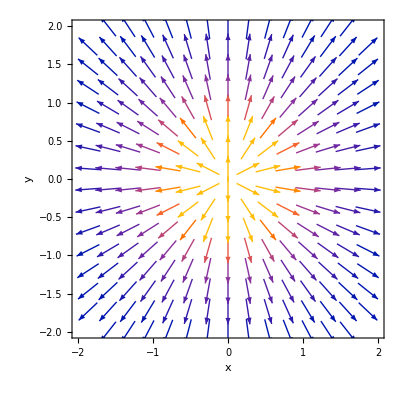

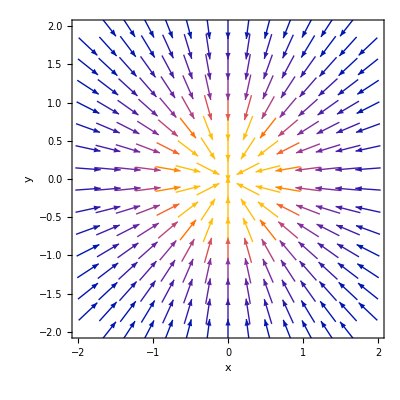

```mathematica
(* Electric Field of a Point Charge *)
ε0=8.854*10^-12;
EField[x_,y_]:=(1/(4 Pi ε0)) q {x,y}/(x^2+y^2)^(3/2);

(* Positive charge *)
q=1*10^-9;
VectorPlot[EField[x,y],{x,-2,2},{y,-2,2},VectorScale->{Small,0.5,None},AxesLabel->{"x","y"}]

(* Negative charge *)
q=-1*10^-9;
VectorPlot[EField[x,y],{x,-2,2},{y,-2,2},VectorScale->{Small,.5,None},AxesLabel->{"x","y"}]
```

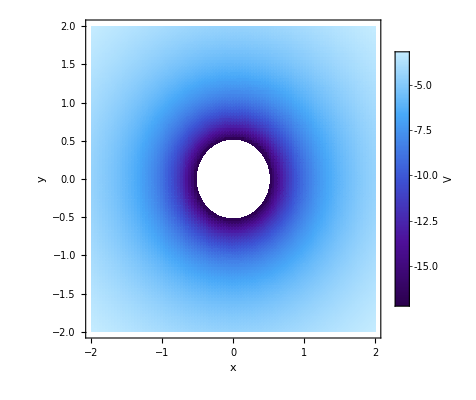

```mathematica
(* Electric Potential of a Point Charge *)
q=-1*10^-9;
V[x_,y_]:=(1/(4 Pi ε0)) q/Sqrt[x^2+y^2];

DensityPlot[V[x,y],{x,-2,2},{y,-2,2},ColorFunction->"DeepSeaColors",AxesLabel->{"x","y"},MaxRecursion->5,PlotPoints->100,PlotLegends->BarLegend[Automatic,LegendLabel->"V"]]
```

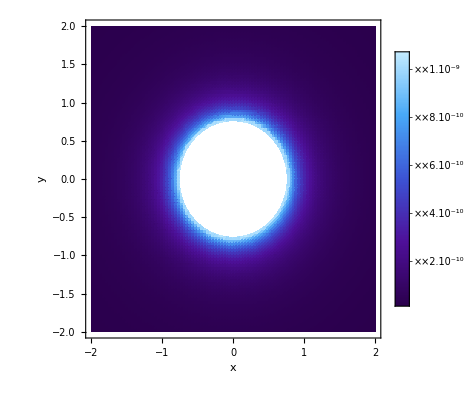

```mathematica
(* Electric Energy Density *)
u[x_,y_]:=(1/2) ε0 Norm[EField[x,y]]^2;

DensityPlot[u[x,y],{x,-2,2},{y,-2,2},ColorFunction->"DeepSeaColors",AxesLabel->{"x","y"},MaxRecursion->5,PlotPoints->100,PlotLegends->BarLegend[Automatic]]
```

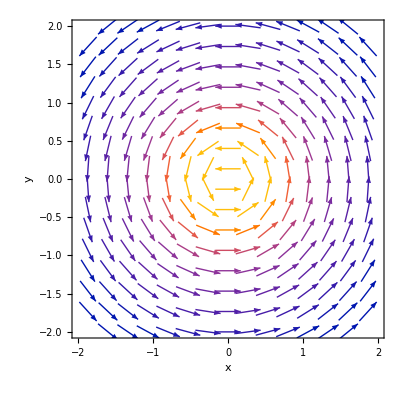

```mathematica
(* Magnetic Field of a Current-Carrying Wire (Biot–Savart Law) *)
μ0=4 Pi*10^-7;
i=1;
BField[x_,y_]:=(μ0 i/(2 Pi (x^2+y^2))) {-y,x};
VectorPlot[BField[x,y],{x,-2,2},{y,-2,2},VectorScale->{Small,0.5,None},AxesLabel->{"x","y"}]
```

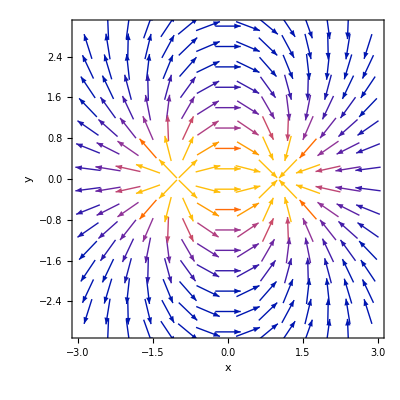

```mathematica
(* Superposition of Electric Dipole Field *)
q1=1*10^-9;q2=-1*10^-9;
r1={-1,0};r2={1,0};
EDipole[x_,y_]:=((1/(4 Pi ε0)) q1 ({x,y}-r1)/Norm[{x,y}-r1]^3+(1/(4 Pi ε0)) q2 ({x,y}-r2)/Norm[{x,y}-r2]^3);

VectorPlot[EDipole[x,y],{x,-3,3},{y,-3,3},VectorScale->{Small,0.5,None},AxesLabel->{"x","y"}]
```

```mathematica
(* Breakdown Maxwell Equation *)
Clear["Global`*"]
k={kx,ky,kz};
fieldH={Hx,Hy,Hz};
fieldE={Ex,Ey,Ez};
-Cross[k,fieldH]==(ω/c).ϵ.fieldE
Cross[k,fieldE]==(ω/c).μ.fieldH
```

{-Hz ky+Hy kz,Hz kx-Hx kz,-Hy kx+Hx ky}==ω/c.ϵ.{Ex,Ey,Ez}

{Ez ky-Ey kz,-Ez kx+Ex kz,Ey kx-Ex ky}==ω/c.μ.{Hx,Hy,Hz}

```mathematica
(* Dispersion solution in a vacuum medium *)
FullSimplify[Solve[Det[{{0,-I k},{I k,0}}-ω {{ϵ,0},{0,μ}}]==0,ω]]//MatrixForm
```

(ω→-k/(√ϵ √μ)
ω→k/(√ϵ √μ))

```mathematica
(* Parameters *)
c=1;
L=2;tmax=2;
E0[x_]:=Exp[-50 (x-1)^2];

(* 1D EM Wave (E-field) *)sol=NDSolve[{D[u[x,t],{t,2}]==c^2 D[u[x,t],{x,2}],u[x,0]==E0[x],Derivative[0,1][u][x,0]==0,u[0,t]==0,u[L,t]==0},u,{x,0,L},{t,0,tmax}];
Manipulate[Plot[Evaluate[u[x,t]/. sol],{x,0,L},PlotRange->All,AxesLabel->{"x","E(x,t)"}],{{t,0,"time"},0,tmax}]
```